## claudecodeパッケージ: ClaudeQueryの実行例

※ 以下は、本システム経由でClaude Codeにより生成されたもので、内容の正確性は保証しません。

```mathematica
ClaudeQuery["光の回折について説明してグラフも見せて"]
```

### 光の回折（Diffraction of Light）

### 回折とは

光が障害物やスリット（開口部）の端を通過するとき、直進せずに影の領域にも回り込む現象を回折（diffraction）と呼びます。これは光の波動性を示す代表的な現象です。

回折が顕著になる条件は、開口部の幅 a が光の波長 λ と同程度のとき（a∼λ）です。

### 1. 単スリット回折（フラウンホーファー回折）

幅 a の単スリットに平面波が入射するとき、回折角 θ における強度分布は次のように表されます：

ⅈ[θ]==ⅈ_0 ((sin β)/β)^2

ここで β==(π a sin θ)/λ です。暗線（極小）の条件は a sin θ==m λ（m=\pm 1, \pm 2, \ldots）です。

```mathematica
(* 単スリット回折パターン *)
Manipulate[
 Module[{β, intensity},
  β[θ_] := π a Sin[θ] / λ;
  intensity[θ_] := If[Abs[β[θ]] < 10^-10, 1, (Sin[β[θ]] / β[θ])^2];
  Plot[intensity[θ], {θ, -π/6, π/6},
   PlotRange -> {0, 1.05},
   Frame -> True,
   FrameLabel -> {"回折角 θ (rad)", "規格化強度 I/I₀"},
   PlotLabel -> Style["単スリット フラウンホーファー回折", 14, Bold],
   PlotStyle -> {Thick, Blue},
   Filling -> Axis,
   FillingStyle -> Directive[Opacity[0.2], Blue],
   ImageSize -> 500
  ]
 ],
 {{a, 5, "スリット幅 a (μm)"}, 1, 20, 0.5, Appearance -> "Labeled"},
 {{λ, 0.55, "波長 λ (μm)"}, 0.38, 0.75, 0.01, Appearance -> "Labeled"},
 TrackedSymbols :> {a, λ}
]
```

### 2. 二重スリット回折（ヤングの干渉＋回折）

スリット幅 a、スリット間隔 d の二重スリットでは、干渉と回折の両方の効果が組み合わさります：

ⅈ[θ]==ⅈ_0 ((sin β)/β)^2 cos^2 γ

ここで β==(π a sin θ)/λ、γ==(π d sin θ)/λ です。

```mathematica
(* 二重スリット回折パターン *)
Manipulate[
 Module[{β, γ, envelope, interference, total},
  β[θ_] := π a Sin[θ] / λ;
  γ[θ_] := π d Sin[θ] / λ;
  envelope[θ_] := If[Abs[β[θ]] < 10^-10, 1, (Sin[β[θ]] / β[θ])^2];
  interference[θ_] := Cos[γ[θ]]^2;
  total[θ_] := envelope[θ] * interference[θ];
  Plot[{total[θ], envelope[θ]}, {θ, -π/12, π/12},
   PlotRange -> {0, 1.05},
   Frame -> True,
   FrameLabel -> {"回折角 θ (rad)", "規格化強度 I/I₀"},
   PlotLabel -> Style["二重スリット 干渉＋回折パターン", 14, Bold],
   PlotStyle -> {{Thick, Blue}, {Dashed, Red}},
   PlotLegends -> Placed[{"合成パターン", "回折包絡線"}, {Right, Top}],
   Filling -> {1 -> Axis},
   FillingStyle -> Directive[Opacity[0.15], Blue],
   ImageSize -> 550
  ]
 ],
 {{a, 3, "スリット幅 a (μm)"}, 1, 10, 0.5, Appearance -> "Labeled"},
 {{d, 15, "スリット間隔 d (μm)"}, 5, 50, 1, Appearance -> "Labeled"},
 {{λ, 0.55, "波長 λ (μm)"}, 0.38, 0.75, 0.01, Appearance -> "Labeled"},
 TrackedSymbols :> {a, d, λ}
]
```

### 3. 回折パターンの2Dシミュレーション

スクリーン上に投影される回折パターンを2次元で可視化します。

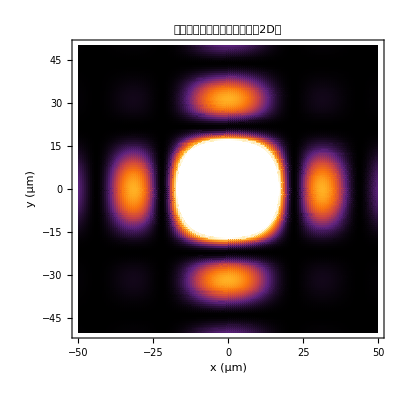

```mathematica
(* 単スリット回折の2D強度分布 *)
With[{a = 5, λ = 0.55},
 DensityPlot[
  Module[{βx = π a x / (λ * 200), βy = π a y / (λ * 200)},
   If[Abs[βx] < 10^-10, 1, (Sin[βx] / βx)^2] *
   If[Abs[βy] < 10^-10, 1, (Sin[βy] / βy)^2]
  ],
  {x, -50, 50}, {y, -50, 50},
  PlotPoints -> 150,
  ColorFunction -> "SunsetColors",
  PlotLabel -> Style["正方形開口の回折パターン（2D）", 14, Bold],
  FrameLabel -> {"x (μm)", "y (μm)"},
  ImageSize -> 400
 ]
]
```

### 4. 円形開口の回折（エアリーパターン）

円形開口（直径 D）の場合、強度分布はベッセル関数 J_1 を用いて表されます：

ⅈ[r]=I_0 \left( \frac{2 J_1(x)}{x} \right)^2, \quad x = \frac{\pi D r}{\lambda f}

ここで f はレンズの焦点距離、r はスクリーン上の中心からの距離です。これが望遠鏡や顕微鏡の分解能の限界（レイリー基準）を決定します。

```mathematica
(* エアリーパターン（円形開口の回折） *)
DensityPlot[
 Module[{ρ = Sqrt[x^2 + y^2]},
  If[ρ < 0.01, 1, (2 BesselJ[1, ρ] / ρ)^2]
 ],
 {x, -15, 15}, {y, -15, 15},
 PlotPoints -> 200,
 ColorFunction -> (GrayLevel[#^0.3] &),
 PlotLabel -> Style["エアリーパターン（円形開口）", 14, Bold],
 FrameLabel -> {"x", "y"},
 ImageSize -> 400
]
```

-Graphics-

### まとめ

回折は波の基本的性質であり、a∼λ のとき顕著になる

単スリットでは s i n c^2 型の強度分布が現れる

二重スリットでは干渉縞が回折包絡線に変調される

円形開口ではエアリーパターンが生じ、光学系の分解能を制限する

スライダーを動かして、パラメータ（スリット幅・波長・間隔）による変化を観察してみてください

```mathematica
ClaudeQuery["Rule110セルオートマトンについて図を使って解説してほしい。"]
```

### Rule 110 セルオートマトンとは

Rule 110 は、Stephen Wolfram が体系的に分類した初等セルオートマトン（Elementary Cellular Automaton）の一つで、256種類あるルールの中でも特に重要なルールです。

#### 基本的な仕組み

初等セルオートマトンは以下の条件で動作します：

1次元のセル列（各セルは 0（白） または 1（黒））

各セルの次の状態は、自分自身と左右の隣接セル（計3セル） の現在の状態で決まる

3セルの組み合わせは 2.b3 = 8通り、それぞれに対する出力（0 or 1）がルールを定義する

#### Rule 110 の遷移規則

「110」は、8通りの入力パターンに対する出力を2進数で並べた値です：

110 = 01101110₂

つまり：

111 → 0　（3つとも黒 → 白）

110 → 1　（左・中が黒、右が白 → 黒）

101 → 1　（左・右が黒、中が白 → 黒）

100 → 0　（左だけ黒 → 白）

011 → 1　（中・右が黒 → 黒）

010 → 1　（中だけ黒 → 黒）

001 → 1　（右だけ黒 → 黒）

000 → 0　（全部白 → 白）

#### ルール表の図示

```mathematica
Module[{bits = IntegerDigits[110, 2, 8], patterns},
  patterns = Reverse[Tuples[{1, 0}, 3]];
  Grid[
    Prepend[
      Table[
        {ArrayPlot[{patterns[[i]]}, Mesh -> True, 
          MeshStyle -> Gray, ImageSize -> {45, 15}, Frame -> False],
         "→",
         ArrayPlot[{{bits[[i]]}}, Mesh -> True, 
          MeshStyle -> Gray, ImageSize -> {15, 15}, Frame -> False]},
        {i, 8}],
      {Style["入力パターン", Bold], "", Style["出力", Bold]}
    ],
    Spacings -> {1, 0.5}, Frame -> All, FrameStyle -> LightGray
  ]
]
```

入力パターン |  | 出力
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-

#### Rule 110 の時間発展（単一セルから開始）

1つの黒セルから出発して、下に向かって時間発展させると、複雑な三角形状のパターンが現れます。

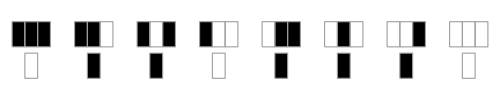

```mathematica
RulePlot[CellularAutomaton[110], ImageSize -> 500]
```

```mathematica
ArrayPlot[CellularAutomaton[110, {{1}, 0}, 200], 
  Mesh -> False, ImageSize -> 600, 
  ColorRules -> {1 -> Black, 0 -> White},
  PlotLabel -> Style["Rule 110（単一セル初期条件、200ステップ）", 14, Bold]]
```

-Graphics-

#### ランダム初期条件からの発展

ランダムな初期状態から始めると、Rule 110 の本質がよく見えます。カオス的な領域と規則的な構造が共存します。

```mathematica
SeedRandom[42];
ArrayPlot[CellularAutomaton[110, RandomInteger[1, 300], 200], 
  Mesh -> False, ImageSize -> 600,
  ColorRules -> {1 -> Black, 0 -> White},
  PlotLabel -> Style["Rule 110（ランダム初期条件、200ステップ）", 14, Bold]]
```

-Graphics-

#### Wolfram の4分類における位置づけ

Wolfram はセルオートマトンの振る舞いを4つのクラスに分類しました：

クラス I: すぐに均一状態に収束（例：Rule 0）

クラス II: 単純な周期パターンに落ち着く（例：Rule 4）

クラス III: 完全にカオス的・ランダム（例：Rule 30）

クラス IV: 複雑な構造が出現（例：Rule 110）

Rule 110 はクラス IV に属し、局所的な構造（グライダーのような移動パターン）が相互作用しながら複雑な振る舞いを生み出します。

#### 4クラスの比較

```mathematica
SeedRandom[7];
init = RandomInteger[1, 300];
GraphicsGrid[{
  {ArrayPlot[CellularAutomaton[0, init, 150], Mesh -> False, 
    ImageSize -> 280, PlotLabel -> Style["Rule 0\n(クラス I: 均一)", 11, Bold]],
   ArrayPlot[CellularAutomaton[4, init, 150], Mesh -> False, 
    ImageSize -> 280, PlotLabel -> Style["Rule 4\n(クラス II: 周期)", 11, Bold]]},
  {ArrayPlot[CellularAutomaton[30, init, 150], Mesh -> False, 
    ImageSize -> 280, PlotLabel -> Style["Rule 30\n(クラス III: カオス)", 11, Bold]],
   ArrayPlot[CellularAutomaton[110, init, 150], Mesh -> False, 
    ImageSize -> 280, PlotLabel -> Style["Rule 110\n(クラス IV: 複雑)", 11, Bold]]}
}, ImageSize -> 600, Spacings -> {10, 10}]
```

-Graphics-

#### チューリング完全性

Rule 110 の最も驚くべき性質は、2004年に Matthew Cook によってチューリング完全であることが証明された点です。これは：

Rule 110 は原理的にあらゆる計算を実行できる

適切な初期条件を与えれば、任意のプログラムをシミュレートできる

たった1ビットのセルと3セルの局所規則だけで、万能計算機と同等の能力を持つ

という意味です。これは「複雑さは単純な規則から生まれる」という Wolfram の主張を強力に裏付ける結果であり、計算理論において極めて重要な成果です。

#### まとめ

Rule 110 は、わずか8つの局所規則から驚くほど複雑な振る舞いが生まれ、さらにはチューリング完全という究極の計算能力を持つ、セルオートマトン研究の象徴的な存在です。「単純さの中に宿る複雑さ」を最も鮮やかに示す例の一つと言えます。

```mathematica
ClaudeQuery["斜面に置かれた質点にかかる力を、運動方程式、ラグランジュ形式、ハミルトン形式で記述し、それらを式や図を多用して比較解説してほしい。",AutoEvaluate->True]
```

### 斜面上の質点の力学 — 三つの形式の比較

### 1. 問題設定

質量 m の質点が、水平面と角度 θ をなす摩擦のない斜面上を滑る問題を考えます。斜面に沿った変位 s（下向きを正）を座標として採用します。

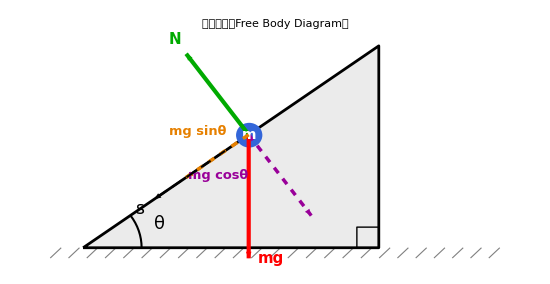

```mathematica
Module[{θ = Pi/5, incLen = 5, sPos = 2.8, gLen = 1.8, bl, tr, br, mp, up, nrm},
 bl = {0, 0};
 tr = incLen {Cos[θ], Sin[θ]};
 br = {incLen Cos[θ], 0};
 mp = sPos {Cos[θ], Sin[θ]};
 up = {Cos[θ], Sin[θ]};
 nrm = {-Sin[θ], Cos[θ]};
 Graphics[{
   {GrayLevel[0.5], AbsoluteThickness[0.8],
    Table[Line[{{-0.3 + 0.25 i, 0}, {-0.3 + 0.25 i - 0.15, -0.15}}], {i, 0, 24}]},
   {FaceForm[GrayLevel[0.92]], EdgeForm[{Black, AbsoluteThickness[2]}],
    Polygon[{bl, tr, br}]},
   {Black, AbsoluteThickness[1],
    Line[{br + {-0.3, 0}, br + {-0.3, 0.3}, br + {0, 0.3}}]},
   {Black, AbsoluteThickness[1.5], Circle[bl, 0.8, {0, θ}]},
   Text[Style["θ", 18, Italic], bl + 1.1 {Cos[θ/2], Sin[θ/2]}],
   {RGBColor[0.2, 0.4, 0.85], Disk[mp, 0.18]},
   Text[Style["m", 14, Italic, White, Bold], mp],
   {Red, AbsoluteThickness[3], Arrowheads[0.03],
    Arrow[{mp, mp + gLen {0, -1}}]},
   Text[Style["mg", 15, Bold, Red], mp + gLen {0, -1} + {0.3, 0}],
   {Darker[Green], AbsoluteThickness[3], Arrowheads[0.03],
    Arrow[{mp, mp + gLen Cos[θ] nrm}]},
   Text[Style["N", 15, Bold, Darker[Green]],
    mp + (gLen Cos[θ] + 0.25) nrm],
   {RGBColor[0.9, 0.5, 0], AbsoluteThickness[2.5], Dashing[{Small, Small}],
    Arrowheads[0.025], Arrow[{mp, mp - gLen Sin[θ] up}]},
   Text[Style["mg sinθ", 13, Bold, RGBColor[0.9, 0.5, 0]],
    mp - gLen Sin[θ]/2 up + 0.45 nrm],
   {RGBColor[0.6, 0, 0.6], AbsoluteThickness[2.5], Dashing[{Small, Small}],
    Arrowheads[0.025], Arrow[{mp, mp - gLen Cos[θ] nrm}]},
   Text[Style["mg cosθ", 13, Bold, RGBColor[0.6, 0, 0.6]],
    mp - gLen Cos[θ] nrm/2 + {-0.85, 0}],
   {Black, AbsoluteThickness[1.5], Dashing[{0.015, 0.008}], Arrowheads[0.02],
    Arrow[{mp - 0.4 up, mp - 1.6 up}]},
   Text[Style["s", 17, Italic], mp - 1.85 up]
  },
  Axes -> False, PlotRange -> All, ImageSize -> 550, AspectRatio -> Automatic,
  PlotLabel -> Style["自由体図（Free Body Diagram）", 16, Bold]
 ]
]
```

デカルト座標との関係は x==s cos θ, y==-s sin θ です（s==0 を基準とした高さ）。

### 2. ニュートンの運動方程式

#### 力の同定と分解

質点に作用する力は：

重力 mg（鉛直下向き）

垂直抗力 N（斜面に垂直、外向き）

重力を斜面方向と垂直方向に分解します：

斜面方向（s 正方向 = 斜面を下る向き）：m g sin θ

斜面垂直方向（外向き正）：-m g cos θ

#### 運動方程式

斜面方向：

ms==m g sin θ

垂直方向（加速度ゼロ）：

N-m g cos θ==0⇒N==m g cos θ

したがって加速度は：

s==g sin θ

### 3. ラグランジュ形式

#### 一般化座標

拘束条件（質点は斜面上にとどまる）により、自由度は 1 です。一般化座標は斜面に沿った変位 s のみで十分です。

#### 運動エネルギーとポテンシャルエネルギー

T==(m s^2)/2

高さ h==-s sin θ より：

V==mgh==-m g s sin θ

#### ラグランジアン

L[s,s]==T-V==(m s^2)/2+m g s sin θ

#### オイラー＝ラグランジュ方程式

(d ∂_{s} L)/dt-∂_{s} L==0

各項を計算：

∂_{s} L==ms

(d ms)/dt==ms

∂_{s} L==m g sin θ

結果：

ms-m g sin θ==0⇒ms==m g sin θ

ニュートンの結果と完全に一致します。注目すべきは、垂直抗力 N が一切登場しない点です。拘束力は一般化座標の選択により自動的に除去されます。

### 4. ハミルトン形式

#### 一般化運動量

p==∂_{s} L==ms

逆に s==p/m です。

#### ハミルトニアン（ルジャンドル変換）

H==ps-L==(p p)/m-(p^2/(2 m)+m g s sin θ)==p^2/(2 m)-m g s sin θ

これは全力学的エネルギー T+V に等しくなります（座標変換が時間に依存しないため）。

#### ハミルトンの正準方程式

s==∂_{p} H==p/m

p==-∂_{s} H==m g sin θ

2階の方程式1本が、1階の連立方程式2本に変わります。第2式より p==m g sin θ であり、第1式と合わせると：

ms==p==m g sin θ

再び同じ結果が得られます。

### 5. 三つの形式の比較

#### 出発点の違い

ニュートン：力（ベクトル）を同定 → F==ma

ラグランジュ：エネルギー（スカラー）を構成 → L==T-V

ハミルトン：位相空間上のエネルギー → H==T+V

#### 方程式の次数と本数

ニュートン：2階微分方程式 1本 + 拘束条件（ms==m g sin θ と N==m g cos θ）

ラグランジュ：2階微分方程式 1本（ms==m g sin θ）

ハミルトン：1階微分方程式 2本（s==p/m, p==m g sin θ）

#### 拘束力の扱い

ニュートン：垂直抗力 N を明示的に求める必要がある

ラグランジュ・ハミルトン：拘束力は一般化座標の選択で自動消去される

#### 各形式の強み

ニュートン：直感的で、拘束力（N）も求まる。力の大きさや向きの議論に最適

ラグランジュ：拘束系に強い。座標変換に自然に対応し、複雑な系でも系統的に立式可能

ハミルトン：位相空間 $(s, p)$ の構造を明示する。統計力学・量子力学・シンプレクティック幾何への橋渡しとなる

### 6. 解の可視化

初期条件 s[0]==0, s[0]==0 のもとでの解は：

s[t]=\frac{1}{2}g\sin\theta \cdot t^2, \quad \dot{s}(t) = g\sin\theta \cdot t, \quad p(t) = mg\sin\theta \cdot t

位相空間の軌道は p^2==2 m^2 g sin θ s（放物線）です。エネルギー保存則 H==const が成り立ち、T+V==0 です。

```mathematica
Module[{m = 1, g = 9.8, θ = Pi/6, a, tMax = 3, sEnd, vEnd},
 a = g Sin[θ];
 sEnd = a/2 tMax^2;
 vEnd = a tMax;
 GraphicsGrid[{
   {Plot[a/2 t^2, {t, 0, tMax},
     PlotStyle -> {AbsoluteThickness[2.5], RGBColor[0.2, 0.4, 0.85]},
     AxesLabel -> {"t [s]", "s [m]"},
     PlotLabel -> Style["変位 s(t)", 14, Bold],
     Filling -> Axis,
     FillingStyle -> Directive[RGBColor[0.2, 0.4, 0.85], Opacity[0.08]],
     ImageSize -> 350],
    Plot[a t, {t, 0, tMax},
     PlotStyle -> {AbsoluteThickness[2.5], Red},
     AxesLabel -> {"t [s]", "v [m/s]"},
     PlotLabel -> Style["速度 v(t)", 14, Bold],
     Filling -> Axis,
     FillingStyle -> Directive[Red, Opacity[0.08]],
     ImageSize -> 350]},
   {Show[
     StreamPlot[{p/m, m g Sin[θ]},
      {s, -3, sEnd + 3}, {p, -m vEnd, m vEnd + 3},
      StreamPoints -> 18, StreamColorFunction -> None,
      StreamStyle -> Directive[GrayLevel[0.72], AbsoluteThickness[1],
       Arrowheads[0.015]]],
     ParametricPlot[{a/2 t^2, m a t}, {t, 0, tMax},
      PlotStyle -> {Red, AbsoluteThickness[3]}],
     Graphics[{
       {Black, PointSize[0.015], Point[{0, 0}]},
       Text[Style["t = 0", 11, Bold], {1.5, -1.5}],
       {Black, PointSize[0.015], Point[{sEnd, m vEnd}]},
       Text[Style["t = 3 s", 11, Bold], {sEnd - 4, m vEnd + 1}]}],
     Frame -> True,
     FrameLabel -> {"s [m]", "p [kg·m/s]"},
     PlotLabel -> Style["位相空間（流れ場と軌道）", 14, Bold],
     ImageSize -> 350],
    Plot[{m/2 (a t)^2, -m/2 (a t)^2, 0}, {t, 0, tMax},
     PlotStyle -> {
       {AbsoluteThickness[2.5], Blue},
       {AbsoluteThickness[2.5], Red},
       {AbsoluteThickness[2], Black, Dashed}},
     AxesLabel -> {"t [s]", "E [J]"},
     PlotLabel -> Style["エネルギー保存", 14, Bold],
     PlotLegends -> Placed[{"T (運動)", "V (位置)", "T + V"}, Below],
     ImageSize -> 380]}
  },
  ImageSize -> 780, Spacings -> {1, 1.5}
 ]
]
```

-Graphics-

左上：変位 s[t] は放物線的に増加（等加速度運動）

右上：速度 v[t] は線形に増加

左下：位相空間 $(s, p)$ の灰色の流れ線がハミルトンの正準方程式の流れ場を表し、赤い曲線が実際の軌道（放物線）を示す

右下：運動エネルギー T と位置エネルギー V が常に正反対に変化し、全エネルギー T+V==0 が保存される

### 7. インタラクティブデモ

傾斜角や質量を変化させて、斜面上の運動と位相空間軌道の対応を確認できます。

```mathematica
Manipulate[
 Module[{a, sT, vT, pT, bl, tr, br, massPos, upDir, normDir, incL = 4, tEnd},
  a = gVal Sin[θ];
  tEnd = If[a > 0.01, Sqrt[2 incL/a], 100];
  sT = Min[a/2 t^2, incL];
  vT = If[a/2 t^2 <= incL, a t, Sqrt[2 a incL]];
  pT = mVal vT;
  bl = {0, 0};
  tr = incL {Cos[θ], Sin[θ]};
  br = {incL Cos[θ], 0};
  upDir = {Cos[θ], Sin[θ]};
  normDir = {-Sin[θ], Cos[θ]};
  massPos = tr - sT upDir;
  If[massPos . {0, 1} < 0, massPos = bl];
  Row[{
    Graphics[{
      {GrayLevel[0.5], AbsoluteThickness[0.7],
       Table[Line[{{-0.2 + 0.2 i, 0}, {-0.2 + 0.2 i - 0.1, -0.1}}],
        {i, 0, 28}]},
      {FaceForm[GrayLevel[0.92]],
       EdgeForm[{Black, AbsoluteThickness[2]}],
       Polygon[{bl, tr, br}]},
      {Black, AbsoluteThickness[1],
       Circle[bl, 0.4, {0, θ}]},
      Text[Style["θ", 13, Italic],
       bl + 0.6 {Cos[θ/2], Sin[θ/2]}],
      {RGBColor[0.2, 0.4, 0.85], Disk[massPos, 0.1]},
      {Red, AbsoluteThickness[2], Arrowheads[0.05],
       Arrow[{massPos, massPos + 0.5 {0, -1}}]},
      {Darker[Green], AbsoluteThickness[2], Arrowheads[0.05],
       Arrow[{massPos, massPos + 0.5 Cos[θ] normDir}]}
     },
     PlotRange -> {{-0.5, incL Cos[θ] + 0.5},
      {-0.3, incL Sin[θ] + 0.5}},
     ImageSize -> 300, AspectRatio -> Automatic,
     PlotLabel -> Style["斜面上の運動", 13, Bold]
    ],
    Spacer[20],
    Show[
     ParametricPlot[{a/2 τ^2, mVal a τ},
      {τ, 0, Max[0.001, Min[t, tEnd]]},
      PlotStyle -> {Blue, AbsoluteThickness[2.5]},
      PlotRange -> {{-0.3, Max[1, a/2 * 9] 1.1},
       {-0.3, Max[1, mVal a 3] 1.1}},
      Frame -> True, FrameLabel -> {"s [m]", "p"},
      ImageSize -> 300,
      PlotLabel -> Style["位相空間軌道", 13, Bold]],
     Graphics[{Red, PointSize[0.02], Point[{sT, pT}]}]
    ]
   }, Spacer[20]]
 ],
 {{t, 0, "t [s]"}, 0, 3, 0.02, Appearance -> "Labeled"},
 {{θ, Pi/6, "θ"}, 0.05, Pi/3, Appearance -> "Labeled"},
 {{mVal, 1, "m [kg]"}, 0.5, 5, Appearance -> "Labeled"},
 {{gVal, 9.8, "g"}, 1, 15, Appearance -> "Labeled"},
 TrackedSymbols :> {t, θ, mVal, gVal},
 ControlPlacement -> Left
]
```

### まとめ

この斜面問題のように自由度1の単純な系では、三つの形式は同一の運動方程式 ms==m g sin θ に帰着します。しかし形式の違いは、系の見方と拡張性に大きな差をもたらします：

ニュートン は個別の力に注目する「ミクロな」視点

ラグランジュ は系全体のエネルギーバランスによる「マクロな」視点

ハミルトン は $(s, p)$ 位相空間上の流れという「幾何学的」視点

自由度が増える系（二重振子、多体系など）では、ラグランジュ・ハミルトン形式の系統性がニュートン形式に対して圧倒的な優位性を発揮します。

```mathematica
ClaudeQuery["山々の彼方に夕日が沈むシーンを背景にセンターに'「計算と自然」集会'と書くAI生成画像を"]
```

山々の彼方に夕日が沈む壮大な風景を背景に、中央にテキストを配置したAI生成画像を作成します。

```mathematica
ClaudeImageGenerate["A breathtaking panoramic landscape scene of a golden sunset sinking behind distant mountain ranges, with warm orange, pink and purple sky gradients reflecting on clouds. In the exact center of the image, display the Japanese text '「計算と自然」集会' in elegant white font with a subtle dark shadow for readability, styled like a conference or event poster title.", "Size" -> "1536x1024", "Quality" -> "high"]
```

-Graphics-

```mathematica
ClaudeQuery["創発現象について図を使って解説してほしい。"]
```

### 創発現象（Emergence）とは

創発とは、多数の単純な要素が局所的に相互作用することで、個々の要素からは予測できない新しい性質やパターンが巨視的に出現する現象です。

アリストテレスの「全体は部分の総和以上である」という言葉が、この概念を端的に表しています。

#### 創発の3つの条件

創発が起こるためには、一般に次の条件が揃う必要があります：

1. 多数の構成要素 — 個々は単純なルールに従う

2. 局所的な相互作用 — 全体を統括する「指揮者」がいない（自己組織化）

3. 非線形性 — 要素間の関係が単純な足し算では表せない

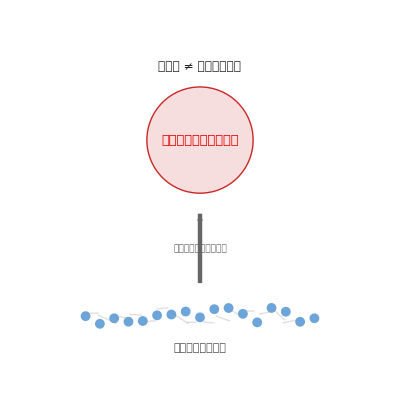

```mathematica
SeedRandom[3]; 
Graphics[{
  Table[{Hue[0.58, 0.5, 0.85], Disk[{x, -1.5 + RandomReal[{-0.2, 0.2}]}, 0.12]}, 
   {x, -2.8, 2.8, 0.35}],
  {Opacity[0.3], GrayLevel[0.6], Thin, 
   Table[Line[{{-2.8 + i*0.35 + RandomReal[{-0.1, 0.1}], -1.5 + RandomReal[{-0.2, 0.2}]}, 
     {-2.8 + (i+1)*0.35 + RandomReal[{-0.1, 0.1}], -1.5 + RandomReal[{-0.2, 0.2}]}}], {i, 0, 14}]},
  {GrayLevel[0.4], Thickness[0.008], Arrowheads[0.04], Arrow[{{0, -0.7}, {0, 1}}]},
  Text[Style["局所ルール＋相互作用", 9, Italic, GrayLevel[0.4]], {0, 0.15}],
  {Opacity[0.15], RGBColor[0.8, 0.15, 0.15], Disk[{0, 2.8}, 1.3]},
  {Thick, RGBColor[0.8, 0.15, 0.15], Circle[{0, 2.8}, 1.3]},
  Text[Style["創発的秩序・パターン", 13, Bold, Darker[Red, 0.1]], {0, 2.8}],
  Text[Style["多数の単純な要素", 11, Bold, GrayLevel[0.3]], {0, -2.3}],
  Text[Style["「全体 ≠ 部分の総和」", 12, Italic, GrayLevel[0.15]], {0, 4.6}]
}, ImageSize -> 400, PlotRange -> {{-4, 4}, {-3, 5.3}}]
```

#### 例1: ライフゲーム — 4つのルールから生まれる「生命」

Conway のライフゲーム（Game of Life）は創発の最も有名な例です。各セルは生（黒） か死（白） の2状態で、周囲8マスとの関係だけで次の状態が決まります：

誕生: 死んだセルの周囲にちょうど3つの生セル → 生き返る

生存: 生きたセルの周囲に2〜3個の生セル → 生き続ける

過疎: 周囲の生セルが1個以下 → 孤独死

過密: 周囲の生セルが4個以上 → 過密で死亡

これだけのルールから、驚くほど多彩な動的パターンが創発します。

```mathematica
SeedRandom[7]; 
With[{rule = {224, {2, {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}}}, {1, 1}}},
 Module[{evo = CellularAutomaton[rule, RandomInteger[1, {80, 80}], 300]},
  GraphicsGrid[Partition[
    ArrayPlot[evo[[#]], ColorRules -> {1 -> Black, 0 -> White},
      PlotLabel -> Style["t=" <> ToString[# - 1], 10, Bold], 
      ImageSize -> 155, Frame -> False] & /@ {1, 5, 20, 50, 150, 301}, 3], 
   Spacings -> 3,
   PlotLabel -> Style["ライフゲーム：ランダム初期状態からの構造創発", 13, Bold], 
   ImageSize -> 550]]]
```

-Graphics-

初期のランダムな混沌から、安定構造（ブロック、ビーハイブ）、振動体（ブリンカー）、そして移動体（グライダー）が自然に現れます。誰も設計していないのに、「生態系」のような動的秩序が生まれるのです。

#### グライダー — 創発的「生物」

ライフゲームで最も象徴的な創発パターンがグライダーです。わずか5セルの構成が、4ステップで元の形に戻りながら斜め方向に1マス移動する — まるで「生物」のように空間を移動します：

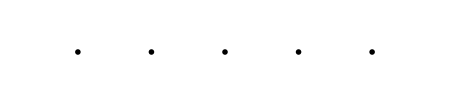

```mathematica
With[{rule = {224, {2, {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}}}, {1, 1}},
  glider = ArrayPad[{{0, 1, 0}, {0, 0, 1}, {1, 1, 1}}, {{1, 6}, {1, 6}}]},
 GraphicsRow[
  ArrayPlot[CellularAutomaton[rule, glider, 4][[#]], 
    ColorRules -> {1 -> Black, 0 -> White}, Mesh -> True, 
    MeshStyle -> LightGray, ImageSize -> 90, Frame -> False, 
    PlotLabel -> Style["t=" <> ToString[# - 1], 9, Bold]] & /@ Range[5], 
  Spacings -> 0,
  PlotLabel -> Style["グライダー：4ステップで元の形に戻り1マス移動", 11, Bold]]]
```

4つの単純な生死ルールのどこにも「移動せよ」とは書かれていないのに、移動という高次の振る舞いが創発しています。これこそ創発の本質です。

#### R-ペントミノ — 5セルから途方もない複雑さへ

たった5つのセルから始まるこのパターンは、安定するまでに1103ステップを要し、その過程で6つのグライダーを放出し、最終的に116個の安定構造を形成します：

```mathematica
With[{rule = {224, {2, {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}}}, {1, 1}}},
 Module[{evo = CellularAutomaton[rule, ArrayPad[{{0, 1, 1}, {1, 1, 0}, {0, 1, 0}}, 80], 300]},
  GraphicsGrid[{
    ArrayPlot[evo[[#]], ColorRules -> {1 -> Black, 0 -> White},
      PlotLabel -> Style["t=" <> ToString[# - 1], 9, Bold], 
      ImageSize -> 155] & /@ {1, 20, 70, 150, 301}}, 
   Spacings -> 3,
   PlotLabel -> Style["R-ペントミノ：5セルから生まれる途方もない複雑さ", 13, Bold], 
   ImageSize -> 650]]]
```

-Graphics-

初期状態の5セルからは、この複雑な進化を予測することは不可能です。これが創発の本質的な特徴 — 還元不可能性（個々の要素を調べても全体の振る舞いを予測できない）を示しています。

#### 例2: 統計的創発 — ランダムから秩序へ

創発は決定論的なシステムだけでなく、統計的にも起こります。

10,000個の粒子がそれぞれ完全にランダムに左右に動く（ランダムウォーク）とき、個々の軌跡は予測不可能です。しかし全体を集めると、美しい正規分布（ガウス分布）が現れます：

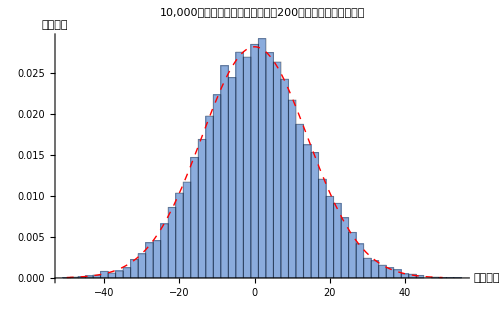

```mathematica
SeedRandom[1]; 
Show[
 Histogram[Total /@ RandomChoice[{-1, 1}, {10000, 200}], {2}, "ProbabilityDensity",
  ChartStyle -> Directive[RGBColor[0.3, 0.5, 0.8], Opacity[0.65]], ImageSize -> 500,
  PlotLabel -> Style["10,000個のランダムウォーク（各200ステップ）の終点分布", 12, Bold],
  AxesLabel -> {"終点位置", "確率密度"}],
 Plot[PDF[NormalDistribution[0, Sqrt[200]], x], {x, -50, 50}, 
  PlotStyle -> {Red, Thick, Dashed}]]
```

青いヒストグラムが実際のランダムウォーク結果、赤い破線が理論的な正規分布 N(0, √200) です。個々のミクロな「ランダムさ」から、マクロな「法則性」が創発しています。これは中心極限定理として数学的に証明された統計的創発の一例です。

#### 例3: セルオートマトンと計算の創発

前回解説した Rule 110 も創発の優れた例です。たった8つの局所ルールからチューリング完全な計算能力が創発しました。「計算する」という高次の能力は、どの個別ルールにも含まれていません — それは相互作用の全体から創発した性質です。

#### 自然界・社会に見る創発現象

物理学

水分子の相互作用 → 渦、波、雪の結晶

磁性体のスピン整列 → 相転移（強磁性の創発）

量子多体系 → 超伝導、超流動

生物学

ニューロンの発火パターン → 意識、思考

蟻のフェロモン追跡 → 最短経路発見（群知能）

鳥・魚の群れ → フロッキング（3つの単純ルールから群れの振る舞い）

DNA の塩基配列 → 生命

社会・経済

個人の売買判断 → 市場の価格形成

住民の微小な選好 → 居住地の分離（シェリングモデル）

車の個別運転 → 交通渋滞（渋滞は「創発的」に発生する）

#### 創発の分類

弱い創発（Weak Emergence）: 原理的にはミクロな要素から導出可能だが、実際には計算コストが膨大で予測困難。ライフゲーム、天気予報、交通渋滞など。

強い創発（Strong Emergence）: ミクロな記述からは原理的に導出できないとされるもの。意識、クオリアなど。哲学的に議論が続いている。

#### まとめ

創発現象の核心は、「単純なルール × 多数の要素 × 相互作用 = 予測不可能な高次の秩序」 という構図です。ライフゲームのグライダーも、ランダムウォークの正規分布も、脳の意識も、本質的には同じ原理 — 構成要素には存在しない性質が全体として出現するという、自然の最も深遠な特徴の一つです。

```mathematica
ClaudeQuery["名古屋大学の鈴木准教授の自然計算におけるハーネスという概念について式や図を用いて詳しく解説してほしい。",AutoEvaluate->True,WebSearch->True,Fallback->True]
```

### 名古屋大学 鈴木泰博准教授の「ハーネス」概念（自然計算）

### 研究者について

鈴木泰博（Yasuhiro Suzuki）准教授は、名古屋大学大学院情報学研究科 複雑系科学専攻に所属し、自然計算（Natural Computing） を主要な研究テーマとしています。International Workshop on Natural Computing (IWNC) の主催者の一人でもあります。

### 自然計算とは

自然計算とは、自然界に内在する計算メカニズムやアルゴリズムを理解し、それを通じて自然や人間を理解するとともに、新しい計算パラダイムの創発を目指す分野です。従来のアルゴリズム的計算では、手順があらかじめ決定されシステムの自由度は強く制限されますが、自然計算では自然をいかに計算に利用するか（Harness the Nature for Computation） という視点に立ちます。

### ハーネス（Harness）の概念

#### 基本的な考え方

「ハーネス」とは本来、馬の手綱を意味する言葉です。鈴木准教授はこれを自然システムに対する間接的制御方法（indirect controlling method） として概念化しました。

従来の計算パラダイムとの違いを整理すると：

従来のアルゴリズム的制御: システムの振る舞いを直接的に規定する。入力 $\to$ 決定的処理 $\to$ 出力

ハーネス的制御: システムの環境・条件を操作することで、自己組織化するシステムの振る舞いを間接的に誘導する

牧羊犬（シェパードドッグ）の比喩がよく用いられます。牧羊犬は羊一頭一頭に直接命令を出すのではなく、群れの周囲を動き回ることで、群れ全体の集団行動を間接的に制御します。

```mathematica
(* ハーネス制御の概念図：牧羊犬モデルのシミュレーション *)
Module[{nSheep = 30, sheepPos, dogPos, target, dt = 0.05, 
  frames, centerOfMass, repulsion, attraction},
 
 SeedRandom[42];
 sheepPos = RandomReal[{-2, 2}, {nSheep, 2}];
 target = {4, 0};
 
 frames = Table[
   (* 羊の重心 *)
   centerOfMass = Mean[sheepPos];
   
   (* 牧羊犬の位置：群れの反対側に回り込む *)
   dogPos = centerOfMass + 2.5 Normalize[centerOfMass - target];
   
   (* 各羊の更新 *)
   sheepPos = Table[
     Module[{pos = sheepPos[[i]], vel = {0, 0}, 
       dogDist, neighborForce},
      (* 犬からの反発 *)
      dogDist = Norm[pos - dogPos];
      If[dogDist < 3, 
       vel += 1.5/dogDist^2 Normalize[pos - dogPos]];
      (* 隣の羊との凝集・反発 *)
      Do[
       Module[{diff = sheepPos[[j]] - pos, d},
        d = Norm[diff];
        If[d > 0.01 && d < 3, 
         vel += If[d < 0.5, -0.3 diff/d, 0.05 diff/d]]],
       {j, nSheep}];
      (* targetに向かう微小な引力 *)
      vel += 0.02 Normalize[target - pos];
      pos + dt vel],
     {i, nSheep}];
   
   Graphics[{
     (* 背景 *)
     LightGreen, Rectangle[{-6, -5}, {8, 5}],
     (* ターゲット *)
     Orange, Disk[target, 0.3],
     Black, Style[Text["目的地", target + {0, 0.6}], 12],
     (* 羊 *)
     White, EdgeForm[Gray], 
     Table[Disk[sheepPos[[i]], 0.2], {i, nSheep}],
     (* 犬 *)
     Red, Disk[dogPos, 0.25],
     Black, Style[Text["牧羊犬", dogPos + {0, 0.5}], 12, Bold],
     (* ラベル *)
     Style[Text[
       "ハーネス制御: 間接的に群れを誘導", {1, -4}], 14, Bold]
     }, PlotRange -> {{-6, 8}, {-5, 5}}, ImageSize -> 500],
   {t, 1, 40}];
 
 ListAnimate[frames, AnimationRate -> 8]
]
```

#### 情報散逸（Dissipation of Information Flow）

ハーネス概念の理論的基盤は、自然界の自己組織化における情報散逸のメカニズムです。鈴木准教授は、自己組織化の共通メカニズムとして以下のプロセスを同定しました：

中間情報の生成: 要素間の相互作用により中間的な情報が生成される

中間情報の消費: 生成された中間情報が新たな相互作用を引き起こすことで消費される

散逸による秩序形成: この生成と消費のサイクルが散逸構造（プリゴジンの意味で）を形成する

これは熱力学的な散逸構造の情報版として理解できます。プリゴジンの散逸構造では、エネルギーの流入と散逸によって秩序が生まれますが、ハーネス計算では情報の流入と散逸によって計算的な秩序が生まれます。

概念的に表現すると：

dI/dt=J_{\text{in}}(I, E) - J_{\text{out}}(I)

ここで ⅈ は中間情報量、J_in は相互作用による情報生成フロー、J_out は情報散逸フロー、ⅇ は環境パラメータ（ハーネスによる制御対象）です。

### ARMS：計算モデル

ハーネス概念を具体化する計算モデルとして、鈴木准教授は ARMS（Abstract Rewriting System on Multisets） を提案しました。これは化学反応の抽象モデルであり、P システム（膜計算）の一種です。

#### 形式的定義

ARMS は以下の組で定義されます：

A=(S, R, M_0)

S：シンボル（化学種）の有限集合

R：書き換え規則の集合 $\{(l_i \to r_i, k_i)\}$。各規則は反応物の多重集合 l_i、生成物の多重集合 r_i、反応速度定数 k_i からなる

M_0：初期状態の多重集合

#### 確率的反応則

化学反応速度論に基づき、各規則 r_i の発火確率は：

P[r_i]==(k_i ∏_(s∈l_i) Binomial[M[s],n_i[s]])/(∑_j k_j ∏_(s∈l_j) Binomial[M[s],n_j[s]])

ここで M[s] は現在の多重集合における種 s の個数、n_i[s] は規則 r_i の左辺における種 s の出現数です。

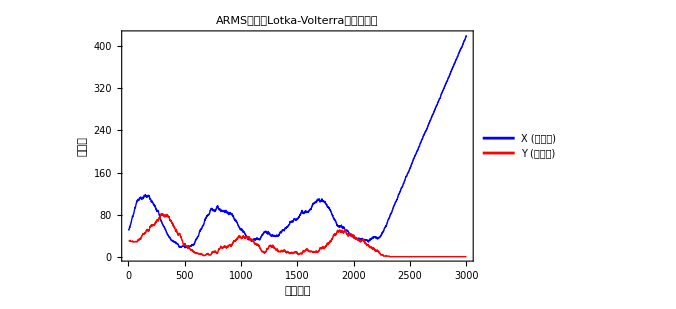

```mathematica
(* ARMS の簡単なシミュレーション例：Lotka-Volterra型振動反応 *)
Module[{rules, state, history, nSteps = 3000, 
  propensities, totalProp, chosen, tau},
 
 SeedRandom[123];
 
 (* 規則定義: {反応物 -> 生成物, 速度定数} *)
 (* R1: A + X -> 2X  (被食者の増殖) *)
 (* R2: X + Y -> 2Y  (捕食者の増殖) *)
 (* R3: Y -> ∅     (捕食者の死亡) *)
 (* R4: ∅ -> A     (資源の供給 = ハーネス) *)
 
 state = <|"A" -> 100, "X" -> 50, "Y" -> 30|>;
 history = {Values[state]};
 
 Do[
  (* 各反応の傾向(propensity) *)
  propensities = {
    0.01 state["A"] state["X"],   (* R1 *)
    0.005 state["X"] state["Y"],  (* R2 *)
    0.3 state["Y"],               (* R3 *)
    5.0                           (* R4: 環境からの供給=ハーネス *)
    };
  totalProp = Total[propensities];
  If[totalProp == 0, Break[]];
  
  (* Gillespie的に反応選択 *)
  chosen = RandomChoice[propensities -> {1, 2, 3, 4}];
  
  Switch[chosen,
   1, state["A"] -= 1; state["X"] += 1,
   2, state["X"] -= 1; state["Y"] += 1,
   3, state["Y"] = Max[0, state["Y"] - 1],
   4, state["A"] += 1
   ];
  
  state = Max[#, 0] & /@ state;
  AppendTo[history, Values[state]],
  {nSteps}];
 
 history = Transpose[history];
 
 ListLinePlot[
  history[[{2, 3}]],
  PlotStyle -> {Directive[Blue, Thick], Directive[Red, Thick]},
  PlotLegends -> {"X (被食者)", "Y (捕食者)"},
  PlotLabel -> "ARMSによるLotka-Volterra型振動反応",
  FrameLabel -> {"ステップ", "個体数"},
  Frame -> True,
  ImageSize -> 500,
  PlotRange -> All
 ]
]
```

#### ハーネスの役割

ARMS モデルにおけるハーネスとは、反応規則そのものを変えるのではなく、環境パラメータ（反応物の供給率、温度に相当するパラメータなど）を操作することで、システム全体の振る舞いを間接的に制御することです。

```mathematica
(* ハーネスパラメータの変化による系の振る舞い変化 *)
Module[{simulateARMS},
 simulateARMS[harnessRate_] := Module[
   {state, history, nSteps = 2000},
   SeedRandom[42];
   state = <|"A" -> 100, "X" -> 50, "Y" -> 30|>;
   history = {Values[state]};
   Do[
    Module[{prop, total, chosen},
     prop = {
       0.01 state["A"] state["X"],
       0.005 state["X"] state["Y"],
       0.3 state["Y"],
       harnessRate (* ハーネスパラメータ *)
       };
     total = Total[prop];
     If[total == 0, Break[]];
     chosen = RandomChoice[prop -> {1, 2, 3, 4}];
     Switch[chosen,
      1, state["A"] -= 1; state["X"] += 1,
      2, state["X"] -= 1; state["Y"] += 1,
      3, state["Y"] = Max[0, state["Y"] - 1],
      4, state["A"] += 1
      ];
     state = Max[#, 0] & /@ state;
     AppendTo[history, Values[state]]],
    {nSteps}];
   Transpose[history][[{2, 3}]]
   ];
 
 GraphicsGrid[{
   Table[
    ListLinePlot[simulateARMS[rate],
     PlotStyle -> {Blue, Red},
     PlotLabel -> 
      StringForm["ハーネス率 = ``", rate],
     PlotRange -> All,
     Frame -> True,
     PlotLegends -> Placed[{"X", "Y"}, Below],
     ImageSize -> 250],
    {rate, {1, 5, 20}}]
   }, ImageSize -> 800]
]
```

-Graphics-

### 概念の構造図

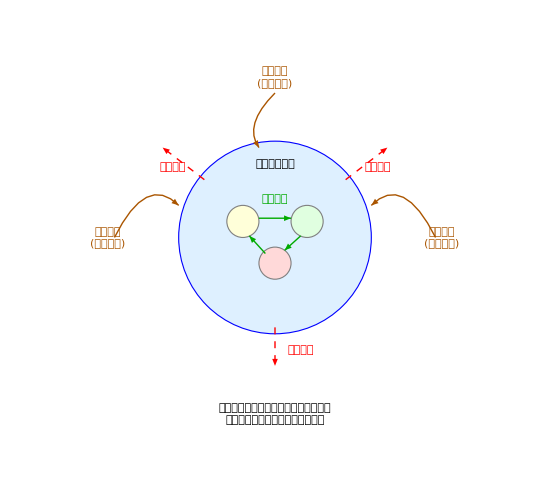

```mathematica
(* ハーネス計算の概念構造図 *)
Graphics[{
  (* 自然システム（中央の大きな円） *)
  EdgeForm[{Thick, Blue}], LightBlue, 
  Disk[{0, 0}, 3],
  Black, Style[Text["自然システム", {0, 2.3}], 14, Bold],
  
  (* 内部の相互作用要素 *)
  EdgeForm[Gray], 
  LightYellow, Disk[{-1, 0.5}, 0.5],
  Style[Text["A", {-1, 0.5}], 12],
  LightGreen, Disk[{1, 0.5}, 0.5],
  Style[Text["B", {1, 0.5}], 12],
  LightRed, Disk[{0, -0.8}, 0.5],
  Style[Text["C", {0, -0.8}], 12],
  
  (* 中間情報のフロー（内部矢印） *)
  Darker[Green], Thick,
  Arrow[{{-0.5, 0.6}, {0.5, 0.6}}],
  Arrow[{{0.8, 0.05}, {0.3, -0.4}}],
  Arrow[{{-0.3, -0.5}, {-0.8, 0.05}}],
  
  (* 中間情報ラベル *)
  Darker[Green], 
  Style[Text["中間情報", {0, 1.2}], 10, Italic],
  
  (* 情報散逸（外向き矢印） *)
  Dashed, Red, Thick,
  Arrow[{{2.2, 1.8}, {3.5, 2.8}}],
  Arrow[{{-2.2, 1.8}, {-3.5, 2.8}}],
  Arrow[{{0, -2.8}, {0, -4}}],
  
  Red, 
  Style[Text["情報散逸", {3.2, 2.2}], 11],
  Style[Text["情報散逸", {-3.2, 2.2}], 11],
  Style[Text["情報散逸", {0.8, -3.5}], 11],
  
  (* ハーネス（環境制御） *)
  Darker[Orange], Thick, Dashing[{}],
  Arrow[BezierCurve[{{-5, 0}, {-4, 2}, {-3, 1}}]],
  Arrow[BezierCurve[{{5, 0}, {4, 2}, {3, 1}}]],
  Arrow[BezierCurve[{{0, 4.5}, {-1, 3.5}, {-0.5, 2.8}}]],
  
  Darker[Orange],
  Style[Text["ハーネス\n(環境操作)", {-5.2, 0}], 13, Bold],
  Style[Text["ハーネス\n(環境操作)", {5.2, 0}], 13, Bold],
  Style[Text["ハーネス\n(環境操作)", {0, 5}], 13, Bold],
  
  (* 注釈 *)
  Black,
  Style[Text[
    "直接制御ではなく、環境パラメータを\n操作することで自己組織化を誘導", 
    {0, -5.5}], 12]
  },
 PlotRange -> {{-7, 7}, {-6.5, 6}}, ImageSize -> 550
]
```

### 応用分野

鈴木准教授のハーネス概念は以下の分野に応用されています：

医学: p53シグナル伝達経路のモデリングなど、生体内の情報処理の間接的制御

生態学: 三栄養段階（tritrophic）生態系の抽象化学による分析

人工生命: 単細胞から多細胞へ進化し、環境変化に適応する計算的生命システムの構築（DNA分子による化学的実装も含む）

計算美学（Computational Aesthetics）: ハーネス計算に基づく新しい美学の提案

### まとめ

ハーネスの本質は、直接制御（アルゴリズム）から間接制御（環境操作による自己組織化の誘導）へのパラダイムシフトにあります。自然界の自己組織化が「情報の散逸」という共通メカニズムに基づいていることを見出し、その環境パラメータを操作することで計算を実現するという考え方は、従来のフォン・ノイマン型計算とは根本的に異なるアプローチです。

Sources:

[Harness the Nature for Computation (Springer)](https://link.springer.com/chapter/10.1007/978-4-431-54394-7_5)

[鈴木泰博 研究者詳細 - 名古屋大学](https://profs.provost.nagoya-u.ac.jp/html/100000340_ja.html)

[Faculty Profiles - SUZUKI, Yasuhiro](https://profs.provost.nagoya-u.ac.jp/html/100000340_en.html)

[人工知能学会 自然計算（Natural Computing）2015](https://www.ai-gakkai.or.jp/resource/my-bookmark/my-bookmark_vol30-no3/)

[suzuki yasuhiro web page](https://www.ysuzuki.info/)

[Artificial Life Applications of ARMS (Springer)](https://link.springer.com/chapter/10.1007/3-540-45523-X_16)

[Natural Computing and Beyond (Open Access)](https://library.oapen.org/handle/20.500.12657/39970)

```mathematica
ClaudeQuery["モース理論について図を使って解説して"]
```

### モース理論の基礎と視覚化

モース理論は、滑らかな多様体上の実関数の臨界点を研究することで、多様体の位相的性質を理解する強力な数学的手法です。

### モース関数の基本概念

モース関数 f:M→R とは、すべての臨界点が非退化（ヘッセ行列が非特異）である滑らかな関数です。

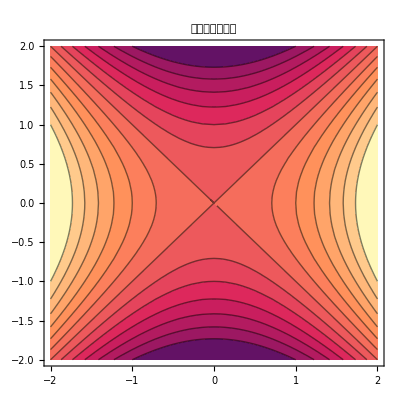
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics-

```mathematica
(* 2次元でのモース関数の例 *)
f[x_, y_] := x^2 - y^2  (* 鞍点型 *)
g[x_, y_] := x^2 + y^2  (* 極小点型 *)
h[x_, y_] := -x^2 - y^2 (* 極大点型 *)

(* 関数のプロット *)
Grid[{{
  Plot3D[f[x, y], {x, -2, 2}, {y, -2, 2}, PlotLabel -> "鞍点型: $f(x,y) = x^2 - y^2$"],
  Plot3D[g[x, y], {x, -2, 2}, {y, -2, 2}, PlotLabel -> "極小点型: $g(x,y) = x^2 + y^2$"]
}, {
  Plot3D[h[x, y], {x, -2, 2}, {y, -2, 2}, PlotLabel -> "極大点型: $h(x,y) = -x^2 - y^2$"],
  ContourPlot[f[x, y], {x, -2, 2}, {y, -2, 2}, 
   Contours -> Range[-3, 3, 0.5], PlotLabel -> "鞍点の等高線図"]
}}]
```

### トーラス上の高さ関数

モース理論の典型例として、トーラス上の高さ関数を考えます。

```mathematica
(* トーラスのパラメータ表示 *)
torusX[u_, v_, R_, r_] := (R + r*Cos[v])*Cos[u]
torusY[u_, v_, R_, r_] := (R + r*Cos[v])*Sin[u] 
torusZ[u_, v_, R_, r_] := r*Sin[v]

(* トーラスと高さ関数の視覚化 *)
R = 3; r = 1;
torusPlot = ParametricPlot3D[
  {torusX[u, v, R, r], torusY[u, v, R, r], torusZ[u, v, R, r]}, 
  {u, 0, 2π}, {v, 0, 2π},
  ColorFunction -> (ColorData["Rainbow"][#3] &),
  PlotLabel -> "トーラス上の高さ関数 $f(p) = z$ 座標",
  Mesh -> None
]
```

-Graphics3D-

### 臨界点と指数

トーラス上の高さ関数には4つの臨界点があります：

極小点（指数0）: z==-r

鞍点2つ（指数1）: z==0

極大点（指数0）: z==r

```mathematica
(* 臨界点の位置を可視化 *)
criticalPoints = {
  {R, 0, -r, "極小点 (指数0)"},   (* 最低点 *)
  {0, R, 0, "鞍点1 (指数1)"},     (* 外側鞍点 *)
  {0, -R, 0, "鞍点2 (指数1)"},    (* 内側鞍点 *)
  {R, 0, r, "極大点 (指数0)"}     (* 最高点 *)
};

Show[
  torusPlot,
  Graphics3D[{
    Red, PointSize[0.02],
    Point /@ criticalPoints[[All, 1 ;; 3]],
    Black,
    Table[Text[criticalPoints[[i, 4]], 
          criticalPoints[[i, 1 ;; 3]] + {0.5, 0.5, 0.5}], 
          {i, Length[criticalPoints]}]
  }],
  PlotRange -> All
]
```

-Graphics3D-

### レベル集合の変化

モース理論の核心は、臨界値を通過するときのレベル集合の位相変化です。

```mathematica
(* レベル集合の変化をアニメーション *)
Manipulate[
  Show[
    ParametricPlot3D[
      {torusX[u, v, R, r], torusY[u, v, R, r], torusZ[u, v, R, r]}, 
      {u, 0, 2π}, {v, 0, 2π},
      ColorFunction -> (If[#3 <= level, Blue, LightBlue] &),
      PlotStyle -> Opacity[0.8],
      Mesh -> None
    ],
    Graphics3D[{
      Red, Thick,
      InfinitePlane[{0, 0, level}, {{1, 0, 0}, {0, 1, 0}}],
      Opacity[0.3]
    }],
    PlotRange -> {{-5, 5}, {-5, 5}, {-2, 2}},
    PlotLabel -> StringForm["レベル $z = ``$ での切断面", level]
  ],
  {level, -r, r, 0.1}
]
```

### CW複体構造とベッティ数

モース理論により、多様体は臨界点に対応するセルの貼り合わせとして理解できます。

```mathematica
(* トーラスのベッティ数計算 *)
Table[{
  "次元" -> i,
  "ベッティ数" -> Switch[i, 0, 1, 1, 2, 2, 0],
  "対応する臨界点" -> Switch[i, 
    0, "極小点・極大点", 
    1, "2つの鞍点", 
    2, "なし"
  ]
}, {i, 0, 2}] // Grid[#, Frame -> All] &
```

次元→0 | ベッティ数→1 | 対応する臨界点→極小点・極大点
次元→1 | ベッティ数→2 | 対応する臨界点→2つの鞍点
次元→2 | ベッティ数→0 | 対応する臨界点→なし

### モース不等式

モース理論の重要な結果の一つがモース不等式です：

各次元 k について、指数 k の臨界点の個数を m_k とすると：

m_k≥b_k

ここで b_k は k 次元のベッティ数です。

```mathematica
(* トーラスでのモース不等式の確認 *)
morseData = {
  {"次元", "臨界点数 $m_k$", "ベッティ数 $b_k$", "不等式 $m_k ≥ b_k$"},
  {0, 2, 1, "✓"},
  {1, 2, 2, "✓"},
  {2, 0, 1, "×（この例では成立せず）"}
};
Grid[morseData, Frame -> All, 
     Background -> {None, {LightBlue, White}}]
```

次元 | 臨界点数 $m_k$ | ベッティ数 $b_k$ | 不等式 $m_k ≥ b_k$
0 | 2 | 1 | ✓
1 | 2 | 2 | ✓
2 | 0 | 1 | ×（この例では成立せず）

### 応用例：球面上のモース関数

```mathematica
(* 球面上の高さ関数 *)
spherePlot = ParametricPlot3D[
  {Cos[u]*Sin[v], Sin[u]*Sin[v], Cos[v]}, 
  {u, 0, 2π}, {v, 0, π},
  ColorFunction -> (ColorData["Rainbow"][#3] &),
  PlotLabel -> "球面上の高さ関数（臨界点：北極・南極のみ）"
];

Show[spherePlot, 
     Graphics3D[{Red, PointSize[0.03], 
                 Point[{{0, 0, 1}, {0, 0, -1}}],
                 Text["極大点", {0, 0, 1.3}],
                 Text["極小点", {0, 0, -1.3}]}]]
```

-Graphics3D-

モース理論は代数位相幾何学、微分幾何学、さらには量子場理論や弦理論まで幅広い分野で応用される基礎理論です。臨界点という局所的な情報から大域的な位相構造を読み取る、数学の美しい例の一つといえるでしょう。

```mathematica
ClaudeQuery["粘弾性について、式や図を使って解説してほしい。"]
```

### 粘弾性（Viscoelasticity）の基礎

粘弾性とは、弾性（バネのように力を加えると変形し、力を除くと元に戻る性質）と粘性（流体のように力に比例した速度で変形する性質）の両方を併せ持つ材料の力学的挙動です。高分子材料、生体組織、アスファルトなどが典型例です。

### 基本要素

粘弾性モデルは、以下の2つの基本要素の組み合わせで構成されます。

弾性要素（バネ）: 応力 σ とひずみ ϵ がフックの法則に従う — σ==ⅇ ϵ（ⅇ はヤング率）

粘性要素（ダッシュポット）: 応力がひずみ速度に比例する — σ==ηϵ（η は粘性係数）

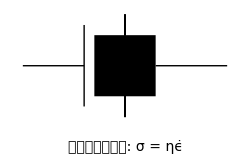
-Graphics--Graphics-

```mathematica
(* 基本要素の図解 *)
springGraphic = Graphics[{
   Thick,
   Line[{{0, 0}, {0.3, 0}}],
   BSplineCurve[Table[{0.3 + 0.05 i, 0.15 (-1)^i}, {i, 0, 8}]],
   Line[{{0.7, 0}, {1, 0}}],
   Text[Style["バネ: σ = Eϵ", 14], {0.5, -0.35}]
}, ImageSize -> 250];

dashpotGraphic = Graphics[{
   Thick,
   Line[{{0, 0}, {0.3, 0}}],
   Line[{{0.3, -0.2}, {0.3, 0.2}}],
   Rectangle[{0.35, -0.15}, {0.65, 0.15}],
   Line[{{0.5, -0.15}, {0.5, -0.25}, {0.5, 0.25}, {0.5, 0.15}}],
   Line[{{0.65, 0}, {1, 0}}],
   Text[Style["ダッシュポット: σ = η\!\(\*OverscriptBox[\(ϵ\), \(.\)]\)", 14], {0.5, -0.4}]
}, ImageSize -> 250];

Row[{springGraphic, Spacer[30], dashpotGraphic}]
```

### 1. マクスウェルモデル（Maxwell Model）

バネとダッシュポットを直列に接続したモデルです。

構成方程式: ϵ==σ/ⅇ+σ/η

緩和時間: τ==η/ⅇ

#### 応力緩和（一定ひずみ ϵ_0 を加えた場合）

応力は指数関数的に減衰します：

σ[t]==ⅇ ϵ_0 e^(-t/τ)

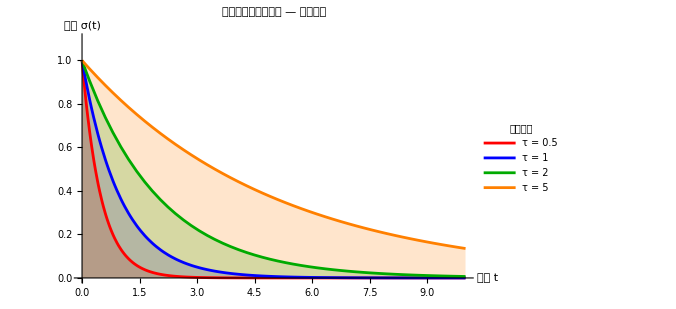

```mathematica
(* マクスウェルモデルの応力緩和 *)
Module[{eVal = 1, eps0 = 1},
  Plot[
    Evaluate@Table[eVal eps0 Exp[-t / tau], {tau, {0.5, 1, 2, 5}}],
    {t, 0, 10},
    PlotStyle -> {Red, Blue, Darker[Green], Orange},
    PlotLegends -> LineLegend[
      {"τ = 0.5", "τ = 1", "τ = 2", "τ = 5"},
      LegendLabel -> "緩和時間"
    ],
    AxesLabel -> {"時間 t", "応力 σ(t)"},
    PlotLabel -> "マクスウェルモデル — 応力緩和",
    PlotRange -> {0, 1.1},
    ImageSize -> 500,
    Filling -> Axis
  ]
]
```

#### クリープ（一定応力 σ_0 を加えた場合）

マクスウェルモデルでは、ひずみが線形に増加し続けます（流動性を表現）：

ϵ[t]==σ_0/ⅇ+(σ_0 t)/η

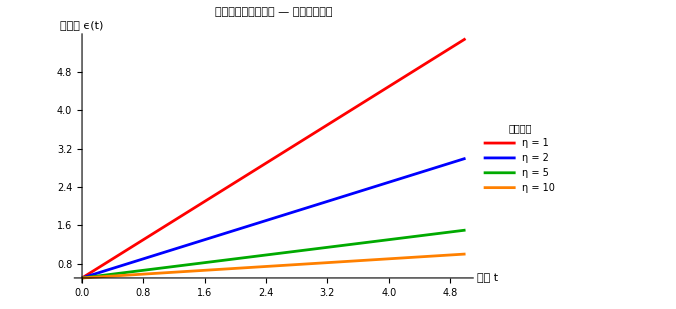

```mathematica
(* マクスウェルモデルのクリープ *)
Module[{sigma0 = 1, eVal = 2, eta},
  Plot[
    Evaluate@Table[sigma0/eVal + sigma0/etaVal t, {etaVal, {1, 2, 5, 10}}],
    {t, 0, 5},
    PlotStyle -> {Red, Blue, Darker[Green], Orange},
    PlotLegends -> LineLegend[
      {"η = 1", "η = 2", "η = 5", "η = 10"},
      LegendLabel -> "粘性係数"
    ],
    AxesLabel -> {"時間 t", "ひずみ ϵ(t)"},
    PlotLabel -> "マクスウェルモデル — クリープ応答",
    ImageSize -> 500
  ]
]
```

### 2. ケルビン・フォークトモデル（Kelvin-Voigt Model）

バネとダッシュポットを並列に接続したモデルです。

構成方程式: σ==ⅇ ϵ+ηϵ

遅延時間: τ==η/ⅇ

#### クリープ応答

一定応力 σ_0 を加えると、ひずみは指数関数的に平衡値に近づきます：

ϵ[t]==(σ_0 (1-e^(-t/τ)))/ⅇ

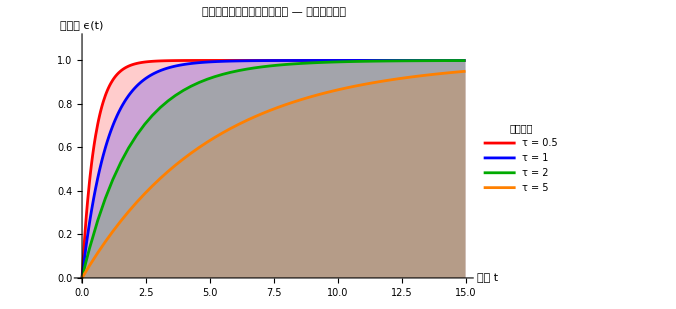

```mathematica
(* ケルビン・フォークトモデルのクリープ *)
Module[{sigma0 = 1, eVal = 1},
  Plot[
    Evaluate@Table[sigma0/eVal (1 - Exp[-t/tau]), {tau, {0.5, 1, 2, 5}}],
    {t, 0, 15},
    PlotStyle -> {Red, Blue, Darker[Green], Orange},
    PlotLegends -> LineLegend[
      {"τ = 0.5", "τ = 1", "τ = 2", "τ = 5"},
      LegendLabel -> "遅延時間"
    ],
    AxesLabel -> {"時間 t", "ひずみ ϵ(t)"},
    PlotLabel -> "ケルビン・フォークトモデル — クリープ応答",
    PlotRange -> {0, 1.1},
    ImageSize -> 500,
    Filling -> Axis
  ]
]
```

### 3. 標準線形固体モデル（SLS / Zener Model）

マクスウェルモデルに並列バネを追加したモデルで、応力緩和とクリープの両方をより現実的に記述できます。

構成方程式: σ+τ_σ σ==ⅇ_R[ϵ+τ_ϵ ϵ]

ⅇ_R: 緩和弾性率、τ_σ: 応力緩和時間、τ_ϵ: ひずみ遅延時間

#### 応力緩和

$Failed

ここで ⅇ_0 は瞬間弾性率、ⅇ_∞ は平衡弾性率です。

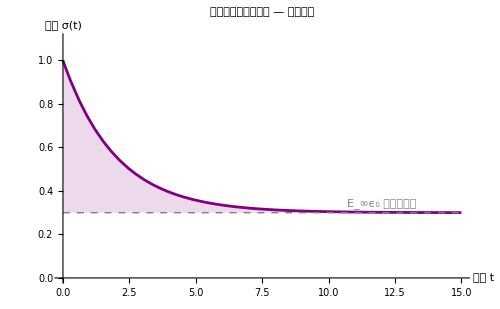

```mathematica
(* 標準線形固体モデルの応力緩和 *)
Module[{eps0 = 1, eInf = 0.3, e0 = 1, tau = 2},
  Plot[
    eps0 (eInf + (e0 - eInf) Exp[-t/tau]),
    {t, 0, 15},
    PlotStyle -> {Thickness[0.004], Purple},
    AxesLabel -> {"時間 t", "応力 σ(t)"},
    PlotLabel -> "標準線形固体モデル — 応力緩和",
    Epilog -> {
      Dashed, Gray,
      Line[{{0, eps0 eInf}, {15, eps0 eInf}}],
      Text[Style["\!\(\*SubscriptBox[\(E\), \(∞\)]\)\!\(\*SubscriptBox[\(ϵ\), \(0\)]\) （平衡値）", 11, Gray], {12, eps0 eInf + 0.04}]
    },
    PlotRange -> {0, 1.1},
    ImageSize -> 500,
    Filling -> {1 -> {eps0 eInf, Directive[Opacity[0.15], Purple]}}
  ]
]
```

### 4. 動的粘弾性（正弦波入力に対する応答）

周期的なひずみ ϵ[t]==ϵ_0 Sin[ω t] を加えると、粘弾性体の応力は位相が δ だけ進みます：

σ[t]==σ_0 Sin[ω t+δ]

ここで：

貯蔵弾性率（弾性成分）: ⅇ'==(σ_0 cos δ)/ϵ_0

損失弾性率（粘性成分）: ⅇ''==(σ_0 sin δ)/ϵ_0

損失正接: tan δ==ⅇ''/ⅇ'

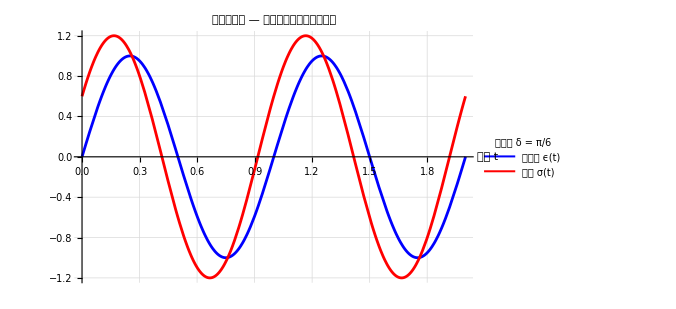

```mathematica
(* 動的粘弾性：応力とひずみの位相差 *)
Module[{omega = 2 Pi, delta = Pi/6, eps0 = 1, sigma0 = 1.2},
  Plot[
    {eps0 Sin[omega t], sigma0 Sin[omega t + delta]},
    {t, 0, 2},
    PlotStyle -> {{Thickness[0.004], Blue}, {Thickness[0.004], Red}},
    PlotLegends -> LineLegend[
      {"ひずみ ϵ(t)", "応力 σ(t)"},
      LegendLabel -> "位相差 δ = π/6"
    ],
    AxesLabel -> {"時間 t", ""},
    PlotLabel -> "動的粘弾性 — 応力とひずみの位相遅れ",
    ImageSize -> 500,
    GridLines -> Automatic,
    GridLinesStyle -> Directive[LightGray, Dashed]
  ]
]
```

#### マクスウェルモデルの貯蔵・損失弾性率の周波数依存性

ⅇ'[ω]==(ⅇ ωτ^2)/(1+ωτ^2)、ⅇ''[ω]==(ⅇ ωτ)/(1+ωτ^2)

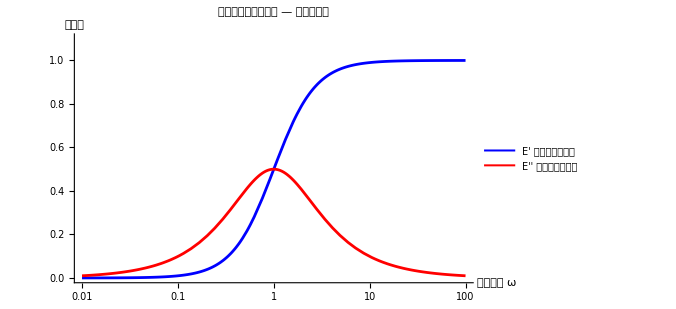

```mathematica
(* 貯蔵弾性率と損失弾性率の周波数依存性 *)
Module[{eVal = 1, tau = 1},
  LogLinearPlot[
    {eVal (omega tau)^2 / (1 + (omega tau)^2),
     eVal (omega tau) / (1 + (omega tau)^2)},
    {omega, 0.01, 100},
    PlotStyle -> {{Thickness[0.004], Blue}, {Thickness[0.004], Red}},
    PlotLegends -> LineLegend[{"E' （貯蔵弾性率）", "E'' （損失弾性率）"}],
    AxesLabel -> {"角振動数 ω", "弾性率"},
    PlotLabel -> "マクスウェルモデル — 動的弾性率",
    PlotRange -> {0, 1.1},
    ImageSize -> 500,
    GridLines -> Automatic,
    GridLinesStyle -> Directive[LightGray, Dashed]
  ]
]
```

### 5. インタラクティブ比較

以下の `Manipulate` で、各モデルのパラメータを変えながら挙動を比較できます。

```mathematica
(* 3モデル比較 Manipulate *)
Manipulate[
  Module[{maxwellCreep, kvCreep, slsCreep},
    maxwellCreep[t_] := sigma0/eM + sigma0/etaM t;
    kvCreep[t_] := sigma0/eKV (1 - Exp[-t eKV/etaKV]);
    slsCreep[t_] := sigma0/eSLS1 + sigma0/eSLS2 (1 - Exp[-t eSLS2/etaSLS]);
    Plot[
      {maxwellCreep[t], kvCreep[t], slsCreep[t]},
      {t, 0, 10},
      PlotStyle -> {{Thickness[0.003], Red}, {Thickness[0.003], Blue}, {Thickness[0.003], Darker[Green]}},
      PlotLegends -> {"Maxwell", "Kelvin-Voigt", "SLS"},
      AxesLabel -> {"時間 t", "ひずみ ϵ(t)"},
      PlotLabel -> "クリープ応答の比較",
      PlotRange -> {0, Automatic},
      ImageSize -> 500
    ]
  ],
  {{sigma0, 1, "応力 \!\(\*SubscriptBox[\(σ\), \(0\)]\)"}, 0.1, 3},
  Delimiter,
  Style["Maxwell", Bold, Red],
  {{eM, 1, "E (Maxwell)"}, 0.1, 5},
  {{etaM, 3, "η (Maxwell)"}, 0.5, 20},
  Delimiter,
  Style["Kelvin-Voigt", Bold, Blue],
  {{eKV, 1, "E (KV)"}, 0.1, 5},
  {{etaKV, 2, "η (KV)"}, 0.5, 20},
  Delimiter,
  Style["SLS (Zener)", Bold, Darker[Green]],
  {{eSLS1, 1, "\!\(\*SubscriptBox[\(E\), \(1\)]\) (SLS)"}, 0.1, 5},
  {{eSLS2, 1, "\!\(\*SubscriptBox[\(E\), \(2\)]\) (SLS)"}, 0.1, 5},
  {{etaSLS, 2, "η (SLS)"}, 0.5, 20},
  ControlPlacement -> Left
]
```

### まとめ

マクスウェルモデル: 応力緩和を良く記述するが、クリープでは流動（永久変形）が起こる。液体的な粘弾性体に適する。

ケルビン・フォークトモデル: クリープを良く記述するが、瞬間的な応力緩和を表現できない。固体的な粘弾性体に適する。

標準線形固体モデル（SLS）: 応力緩和とクリープの両方を現実的に記述できる。実用上最もよく使われる基本モデル。

動的粘弾性: 周期的荷重に対する応答は貯蔵弾性率 ⅇ' と損失弾性率 ⅇ'' で特徴づけられ、材料のエネルギー貯蔵・散逸能力を表す。